# 27: Rayleigh Quotient and Inverse Iteration

For the next few lectures A∈ℝ^(m×m) is symmetric A=Aᵀ.  This means that A is orthogonally diagonalizable with real eigenvalues i.e.
	A=Q.Λ.Qᵀ
with Q=(q_1 | | | q_2 | | | … | | | q_m) satisfying A.q_i=λ_i q_i with Λ=dia(λ_1,λ_2,…,λ_m).

## Rayleigh Quotient

Critical points v of the Rayleigh quotient
	r(x)=(x.A.x)/(x.x)
are eigenvectors of A with eigenvalues r(v).   This is immediate once you differentiate r(x)
	∇r(x).b=((b.A.x + x.A.b) (x.x)-(x.A.x)(x.b + b.x))/(x.x)^2=(2(x.A.b) (x.x) - 2(x.A.x)(x.b))/(x.x)^2
which gives
	∇r(x)=2 (x.x)^-2(A.x-r(x) x).
We can look at this in a projected contour plot in any dimension.

```mathematica
m=6; A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
r[A_,x_]:= x.A.x/(x.x)
V=Eigenvectors[A];
{u1,u2}=Map[Normalize,RandomReal[{-1,1},{2,m}]];
TabView[
Table[ContourPlot[r[A,V⟦i⟧+ϵ1 u1 +ϵ2 u2],{ϵ1,-0.5,0.5},{ϵ2,-0.5,0.5},
Contours->54,PlotPoints->50,Epilog->{Red,Point[{0,0}]}],
{i,m}]]
```

123456

In 3D we can see the critical points almost all at once on the surface of the unit sphere.

```mathematica
r[A_List,x_List]:= x.A.x/(x.x)
m=3; A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
{λs,V}=Eigensystem[A];
{λMin,λMax}={Min[λs],Max[λs]};
MyMesh =DiscretizeRegion[Sphere[{0,0,0},1]];
{pts,cells}={MeshCoordinates[MyMesh],MeshCells[MyMesh,2]};
colors =Map[Hue[0.9(#.A.#-λMin)/(λMax-λMin)]&,pts];
Pic=Graphics3D[{{PointSize[0.02],Point[V]},GraphicsComplex[pts,cells,VertexColors->colors]}];
TabView[{
1->Show[Pic, ViewPoint->2 V⟦1⟧],
2->Show[Pic, ViewPoint->2 V⟦2⟧],
3->Show[Pic, ViewPoint->2 V⟦3⟧],
-1->Show[Pic, ViewPoint->-2 V⟦1⟧],
-2->Show[Pic, ViewPoint->-2 V⟦2⟧],
-3->Show[Pic, ViewPoint->-2 V⟦3⟧]
}]
```

123456

## Functions for Iterative Procedures

For our QR, LU etc. algorithms we knew when we were done!  In the iterative scripts below we are going to mess around until it looks done! Functions implementing iterative schemes need to decide when to stop!  We are going to leave this tricksy issue (and writing such functions) until later.

The number of steps a scheme takes to converge to a specified tolerance is important.  We are going to look at some simple schemes and get a feel for how many steps they take to converge.

## Power Iteration

Power iteration improves an approximation for the eigenvector associated with the largest eigenvalue repeatedly multiplying by the matrix and normalizing. It is pretty simple.  You can see the convergence of the eigenvector and the Rayleigh quotient! This is our first “iterative” schemes.

### Script

```mathematica
m=6;A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
r[A_][x_]:=x.A.x 
λs=Eigenvalues[A]
MaxIter=44;
v0=Normalize[RandomReal[{-1,1},m]];
vData=NestList[Normalize[A.#]&,v0,MaxIter];
λData=Map[r[A],vData];
TabView[{
"vecs"->MatrixPlot[vData],
"vals"->ListPlot[λData,
FrameLabel->{"iter","λ"},GridLines->{Automatic,λs},PlotRange->All,Frame->True],
"err"->ListLogPlot[Abs[λData-λs⟦1⟧],
FrameLabel->{"iter","err"},GridLines->Automatic,Frame->True]
}]
```

{-3.65057,3.01394,2.29452,1.79091,-1.73362,0.0921992}

123

#### Convergence:

For real symmetric A we have A=Q.Λ.Qᵀ.  We can put the “big” eigenvalues first i.e. we order the eigenvalues so that |λ_i|≥|λ_(i+1)| and write our initial guess x_0 in the orthogonal eigenvalue basis q_1,q_2,…,q_m. Entirely equivalently we can simply transform to the basis in which A is diagonal (the eigenvalue basis) and think about applying the power method with just the diagonal matrix Λ.  This looks cleaner to me so we are going to do it.

We are going to skip the normalization step at first.  The iteration without normalization 
in the eigenvector basis is simply
	  |   | x_0 | = | {α_1,α_2,α_3,…,α_m}
x_1 | = | Λ.x_0 | = | {λ_1 α_1,λ_2 α_2,λ_3 α_3,…,λ_m α_m}
x_2 | = | Λ.x_1 | = | {λ_1^2 α_1,λ_2^2 α_2,λ_3^2 α_3,…,λ_m^2 α_m}
  |   |   | ⋮ |  
x_k | = | Λ.x_(k-1) | = | {λ_1^k α_1,λ_2^k α_2,λ_3^k α_3,…,λ_m^k α_m}
  |   |   | ⋮ |  
If we assume λ_1 is separated from the λ_2 in size say|λ_1|=|λ_2|(1+δ) then eventually 
	x_k={λ_1^k α_1,λ_2^k α_2,λ_3^k α_3,…,λ_m^k α_m}∼{λ_1^k α_1,0,0,…,0}
and we could estimate the difference using δ like this 
	||x_k-{λ_1^k α_1,0,0,…,0}(||)^2=||{0,λ_2^k α_2,λ_3^k α_3,…,λ_m^k α_m}(||)^2=∑_(i=2)^m (|λ_i|)^(2k)(α_i)^2≤(|λ_2|)^(2k)∑_(i=2)^m α_i^2.
Things in here get big if λ_1 is big and small is λ_1is small! We need to normalize!
	((||x_k-{λ_1^k α_1,0,0,…,0}||)/(|λ_1|)^(2k))^2≤((|λ_2|)/(|λ_1|))^(2k)∑_(i=2)^m α_i^2=(1/(1+δ))^(2k)∑_(i=2)^m α_i^2
Normalizing at every step does not change much.  We should be able to see this convergence.  There is one minor complication: there are two possible real eigenvectors that differ by a factor of “-1”.  This is easy enough to fix but the code looks a little weird.

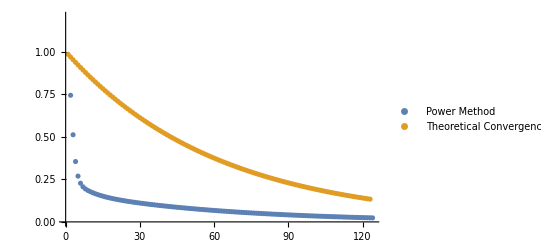

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
{{λ1,λ2},{v1,v2}}=Eigensystem[A,2];
x0=RandomReal[{-1,1},m];
MaxIter=123;
PowerMethodData=NestList[Normalize[A.#]&, x0, MaxIter];
δ=Abs[λ1]/Abs[λ2]-1;
CompData=Table[(1+δ)^-i,{i,1,MaxIter}];
ListPlot[{
Map[ Min[Norm[#-v1],Norm[#+v1]]&, PowerMethodData],
CompData
},
PlotLegends->{"Power Method","Theoretical Convergence"}]
```

If the ±eigenvector thing bothers you we can look at the Rayleigh quotient that converges to the eigenvalue.  The Rayleigh quotient converges faster than the underlying eigenvector!

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
{{λ1,λ2},{v1,v2}}=Eigensystem[A,2];
δ=Abs[λ1]/Abs[λ2]-1;
x0=RandomReal[{-1,1},m];
MaxIter=64;
PowerMethodData=NestList[Normalize[A.#]&, x0, MaxIter];
CompData=Table[(1+δ)^-i,{i,1,MaxIter}];
TabView[{
"RayleighQuotient"->ListPlot[{
Map[#.A.#&, PowerMethodData]
},
GridLines->{Automatic,{λ1,λ2}},
PlotLegends->{"Power Method","Theoretical Convergence"}],
"Convergence"->ListLogPlot[{
Abs[Map[#.A.#&, PowerMethodData]-λ1],
CompData^2
},
GridLines->{Automatic,{λ1,λ2}},
PlotLegends->{"Power Method","Theoretical Convergence"}]
}]
```

12

## Inverse Power Iteration

Inverse Power iteration improves an approximation for the eigenvector associated with the “smallest” eigenvalue repeatedly multiplying by the “inverse” of the matrix and normalizing. It is pretty simple.  You can see the convergence of the eigenvector and the Rayleigh quotient!

#### Convergence:

For real symmetric A convergence to the “smallest” eigenvector is controlled by the gap between 1/λ_m and 1/λ_(m-1) since those are the biggest eigenvalues of A^-1.

### Script

```mathematica
m=6;A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
r[A_][x_]:=x.A.x 
λs=Eigenvalues[A]
MaxIter=34;
v0=Normalize[RandomReal[{-1,1},m]];
LinSol=LinearSolve[A];
vData=NestList[Normalize[LinSol[#]]&,v0,MaxIter];
λData=Map[r[A],vData];
TabView[{
"vecs"->MatrixPlot[vData],
"vals"->ListPlot[λData,
FrameLabel->{"iter","λ"},GridLines->{Automatic,λs},PlotRange->All,Frame->True],
"err"->ListLogPlot[Abs[λData-λs⟦-1⟧],
FrameLabel->{"iter","err"},GridLines->Automatic,Frame->True]
}]
```

{-4.10381,3.64829,-2.34442,1.29217,-0.476419,-0.276202}

123

## Shifted Inverse Power Iteration

Shifted Inverse Power iteration improves an approximation for the eigenvector associated with the eigen value near a specified target μ (called a shift) by repeatedly multiplying by (A-μ I)^-1 and normalizing. It is pretty simple.  You can see the convergence of the eigenvector and the Rayleigh quotient!

#### Convergence:

For real symmetric A convergence to the “nearest” eigenvector to μ is controlled by the gap between the largest and second largest of the shifted reciprocal eigenvalues 1/(λ_i-μ). The nearer you are to an eigenvalue the faster it converges.

### Script

```mathematica
m=6;A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
r[A_][x_]:=x.A.x 
λs=Eigenvalues[A]
```

{-2.84399,-2.27075,1.97872,-0.874327,0.825127,0.244246}

We need to pick a target!

```mathematica
μ=0.8;
MaxIter=34;
v0=Normalize[RandomReal[{-1,1},m]];
LinSol=LinearSolve[A-μ IdentityMatrix[m]];
vData=NestList[Normalize[LinSol[#]]&,v0,MaxIter];
λData=Map[r[A],vData];
TabView[{
"vecs"->MatrixPlot[vData],
"vals"->ListPlot[λData,
FrameLabel->{"iter","λ"},GridLines->{Automatic,λs},PlotRange->All,Frame->True],
"err"->ListLogPlot[Abs[λData-λData⟦-1⟧],
FrameLabel->{"iter","err"},GridLines->Automatic,Frame->True]
}]
```

123

## Rayleigh Quotient Iteration

Rayleigh quotient iteration improves an approximation for the eigenvector associated with the eigenvalue near a specified initial target μ_0 by repeatedly multiplying by (A- μ_k I)^-1and normalizing. It is slightly more complicated before because we need to keep track of the shift μ as well as the vector.  You can see the convergence of the eigenvector and the shift below!

#### Convergence:

For real symmetric A convergence at each step is controlled by the gap between the largest and second largest of the shifted reciprocal eigenvalues 1/(λ_i-μ_k). The nearer you are to an eigenvalue the faster it converges. Since the Rayleigh quotient estimates eigenvalues this usually converges very fast to some eigenvector eigenvalue pair.

### Script

```mathematica
m=23;A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
r[A_][x_]:=x.A.x 
λs=Eigenvalues[A]
RQStep[A_][{μ_,v_}]:= Module[{vNew},
vNew=Normalize[LinearSolve[A-μ IdentityMatrix[Length[A]],v]];
{vNew.A.vNew,vNew}]
```

{-6.95657,6.45819,-6.36142,6.33883,-5.20702,5.12118,4.91952,-3.9914,-3.88401,3.57372,-3.55789,3.39442,2.62673,-2.47478,-2.16996,2.14331,-1.93577,1.80058,-1.28793,1.22771,1.0143,-0.794934,0.697613}

We need to pick a target!

```mathematica
μ0=2.6;
MaxIter=123;
v0=Normalize[RandomReal[{-1,1},m]];
μvData=NestList[RQStep[A],{μ0,v0},MaxIter];
{μData,vData}=μvDataᵀ;
errs=Map[ Min[Abs[λs-#]]&,μData];
TabView[{
"vecs"->MatrixPlot[vData,FrameLabel->{"iter","comp"}],
"shifts"->ListPlot[μData,
FrameLabel->{"iter","μ"},PlotRange->{Min[λs],Max[λs]},
Frame->True,GridLines->{Automatic,λs}],
"err"->ListLogPlot[errs,
FrameLabel->{"iter","err"},GridLines->Automatic,Frame->True]
}]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-1.9693,0.805767,1.78123,0.42725,-1.16896,0.276432,1.04072,-0.744882,0.261652,0.268264,«13»},«9»,«13»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

123

It usually converges really fast.  It usually (but not always) converges to the nearest eigenvalue.